```mathematica
SetDirectory[NotebookDirectory[]];
dichotomy ="dichotomy.dat";
golden = "golden.dat";
Results={Flatten@Import[dichotomy], Flatten@Import[golden]} ;
```

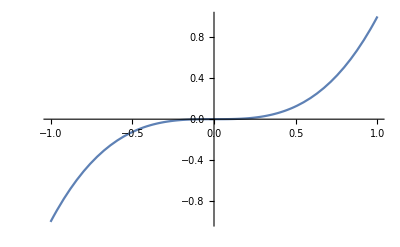

```mathematica
Plot[x *x *x, {x, -1, 1}]
```

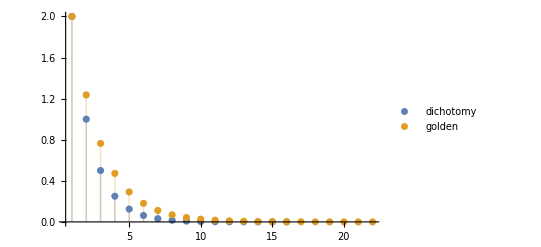

```mathematica
ListPlot[Results, PlotLegends->{"dichotomy", "golden"}, PlotRange->All, Filling->Axis]
```